```mathematica
u=(1-ⅇ^(2 ⅈ ξ)-α+ⅇ^(ⅈ ξ) α)/(1/12 ⅇ^(2 ⅈ ξ) (-4-α)+2/3 ⅇ^(ⅈ ξ) (-2+α)+1/12 (-4+5 α));
```

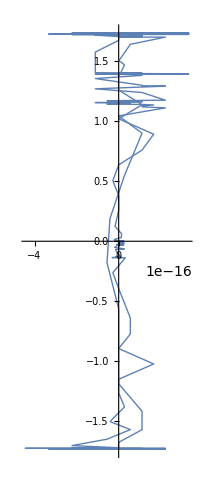

```mathematica
α=0;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
```

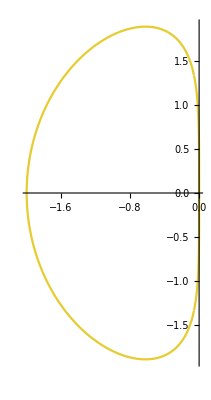

```mathematica
α=0.5;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.9,0.8,0.19]
,AxesOrigin->{0,0}
,PlotRange->All]
```

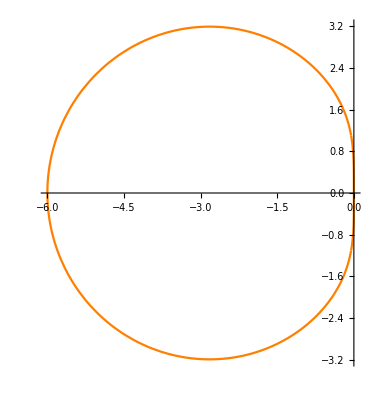

```mathematica
α=1;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Orange
,AxesOrigin->{0,0}
,PlotRange->All]
```

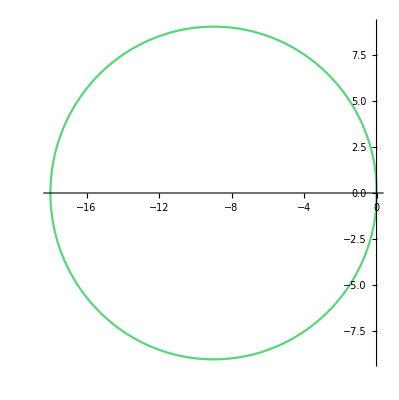

```mathematica
α=1.5;
p4=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.34,0.84,0.48]
,AxesOrigin->{0,0}
,PlotRange->All]
```

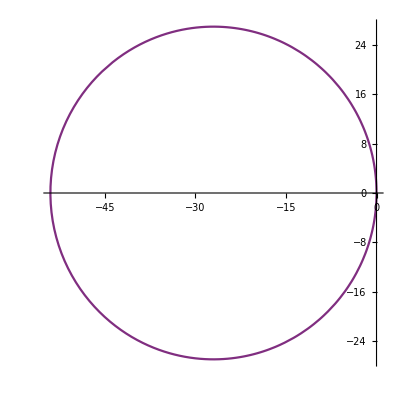

```mathematica
α=1.8;
p5=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.5,0.18,0.5]
,AxesOrigin->{0,0}
,PlotRange->All]
```

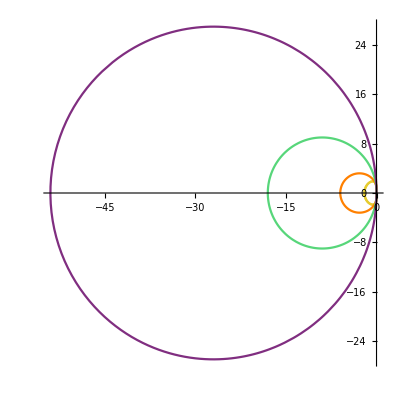

```mathematica
Show[p1,p2,p3,p4,p5]
```

```mathematica
Show[%137,ImageSize->Large]
```

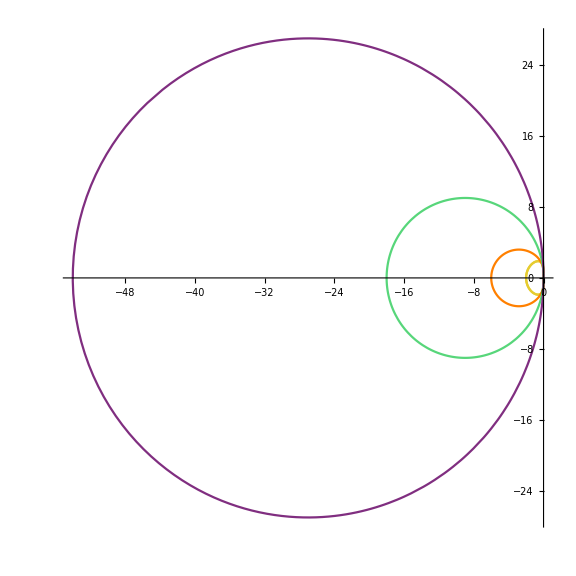

-Graphics-

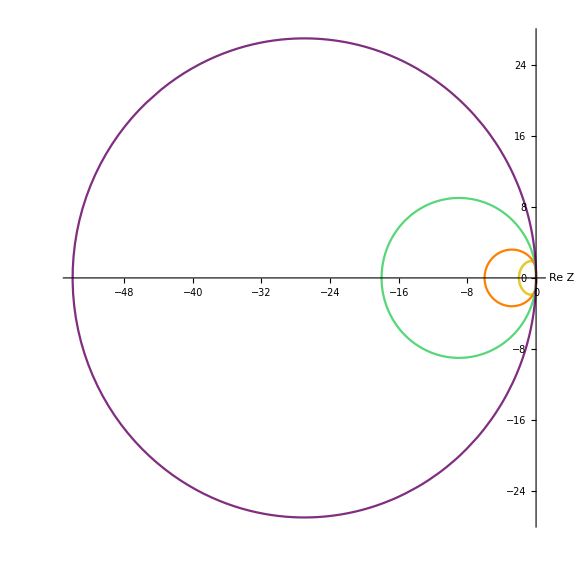

```mathematica
Show[%1,AxesLabel->{HoldForm[Re Z],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%10,AxesLabel->{HoldForm[Re Z],HoldForm[Im Z]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

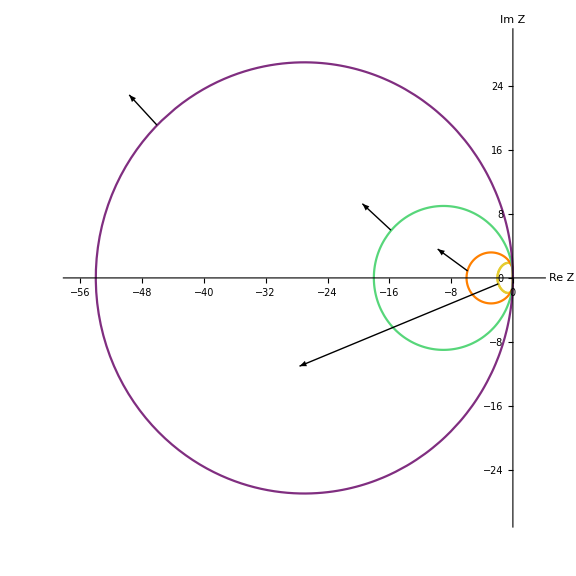

```mathematica
Show[%80,PlotLabel->None,LabelStyle->{18,GrayLevel[0]},AxesLabel->{Style[Re Z,Medium],Style[Im Z,Medium]},AxesStyle->{{Arrowheads[0.03],AbsoluteThickness[1]}, {Arrowheads[0.03],AbsoluteThickness[1]}}]
```

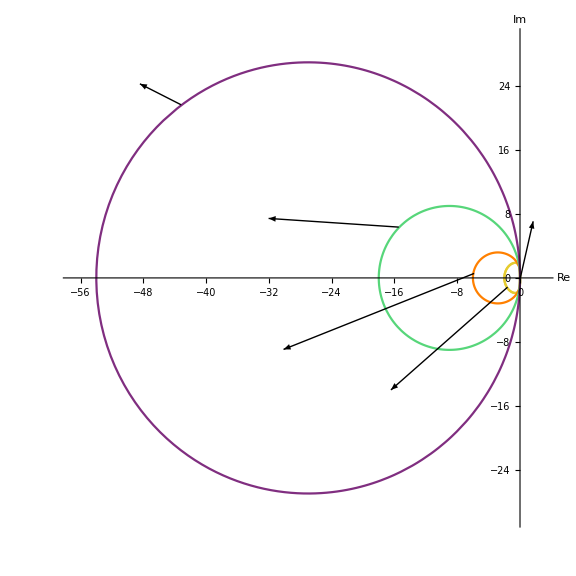

-Graphics-

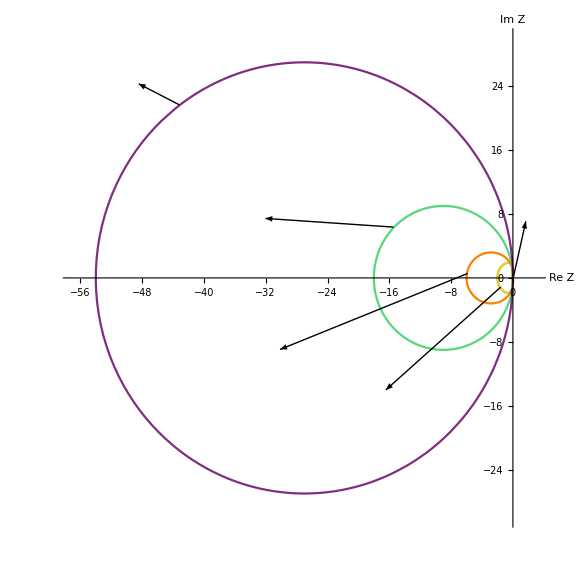

```mathematica
-Graphics-
Show[%2,PlotLabel->None,LabelStyle->{18,GrayLevel[0]},AxesLabel->{Style[Re Z,Medium],Style[Im Z,Medium]}]
```

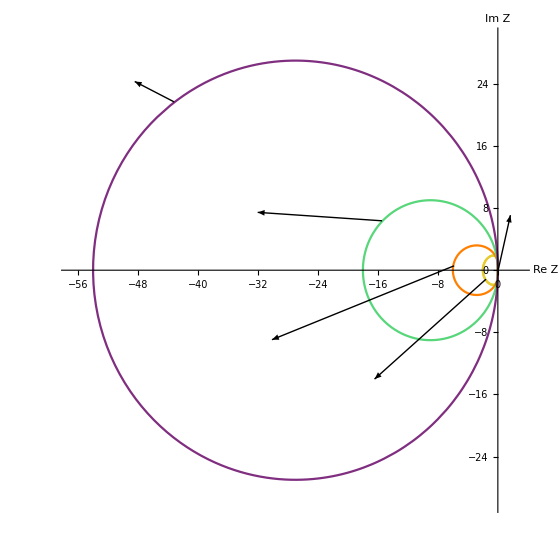

```mathematica
Show[%4,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```